Зад. 1 Функцията на Рунге f(x) = 1/(1+25 x^2) е апроксимирана с полиномите:
p_4(x) = 1 - 4.22719 x^2+3.31565 x^4 
и
p_10(x)=1 - 16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10.

Да се намерят и сравянт рваномерните и средноквадратичните разстояния при тегло μ(x) = 1 в интервала [-1,1] между f и двата полнома.

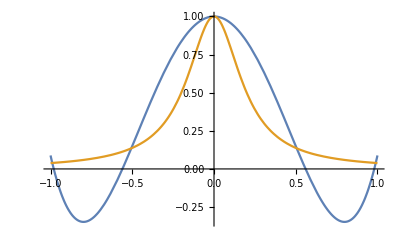

```mathematica
Plot[{1-4.22719 x^2+3.31565 x^4,1/(1+25 x^2)},{x,-1,1}]
```

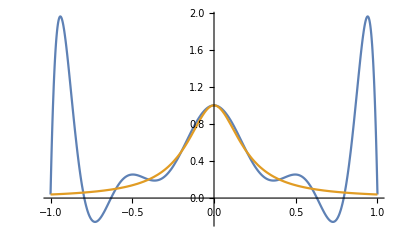

```mathematica
Plot[{1-16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10,1/(1+25 x^2)},{x,-1,1}]
```

Зад. 2 Да се намери полиномът на най-добро средноквадратично приближение от втора степен в интервала [0, 1.5] за функцията f(x) = e^x при тегло μ(x) = 1.

Зад. 3 Като се използва факта, че най-доброто решение x на преопределената система А x = b,
удовлетворява матричното уравнение 

A^Т A x = А^Тb,

да се реши системата
x - y = 1
x + y = 1
x + y = -1
x - y = -1.